```mathematica
(*Taylor - aproskimacija*)
```

```mathematica
Clear[f,n]
```

```mathematica
f[t_]:=Sin[t]*t^2*E^-t
```

```mathematica
Manipulate[Show[
Plot[f[t],{t,0,4},PlotStyle->Red,AxesLabel->{"x","y"},PlotLegends->{"f(t)"}],
Plot[Evaluate[Normal[Series[f[t],{t,2,n}]]],{t,0,4},PlotStyle->Blue, AxesLabel->{"x","y"},PlotLegends->{"Taylor n=" <>ToString[n]}],PlotRange->All],
{n,1,10,1}]
```

```mathematica
(*Izračunan približek π*)
```

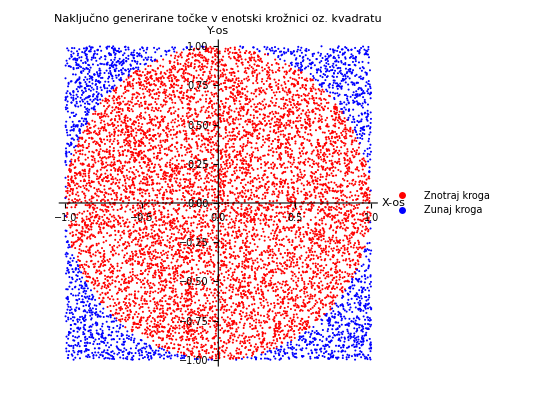

```mathematica
Get["C:\\Users\\marce\\OneDrive\\Desktop\\3. letnik - zimski semester\\NROR\\DN2\\Datotečna funkcija.nb"];
{vKrogu,izvenKroga}=Datoteka[10000];
{piAproks,napaka}=areaPi[nInKrogu,10000];
Show[ListPlot[{vKrogu,izvenKroga},PlotStyle->{Red,Blue},PlotLegends->{"Znotraj kroga","Zunaj kroga"},AxesLabel->{"X-os","Y-os"},PlotLabel->"Naključno generirane točke v enotski krožnici oz. kvadratu",AspectRatio->Automatic]]
```